```mathematica
Clear["Global`*"];
$Version
```

14.0.0 for Microsoft Windows (64-bit) (December 13, 2023)

```mathematica
dropPath=Take[(FileNameSplit /@ # ) //Transpose,-1][[1]]&;
```

```mathematica
SetDirectory[NotebookDirectory[]];
here=NotebookDirectory[];
FileNames["*",here] //dropPath
```

{JAMpolPDF.nb,LHAPDF,MP_packages,PDFDATA,PDFdata15.csv}

```mathematica
dirFilesLHA="./LHAPDF";
dirList=FileNames["*",dirFilesLHA];
```

```mathematica
dirPackages=here<>"MP_packages";
Get[dirPackages<>"/pdfParseLHA.m"];
Get[dirPackages<>"/pdfParseCTEQ.m"];
Get[dirPackages<>"/pdfErrors.m"];
```

Version: pdfCalc 5.0

Version: ManeParse 5.0: April 2021

- Required Package: pdfCalc --Loaded -

===============================================================

- pdfParseLHA -

Version:  5.0: April 2021

Authors: E.J. Godat, D.B. Clark & F.I. Olness

Please cite: **************

http://ncteq.hepforge.org/code/pdf.html

For a list of available commands, enter: ?pdf*

===============================================================

===============================================================

- pdfParseCTEQ -

Version:  5.0:  April 2021

Authors: D.B. Clark, E.J. Godat & F.I. Olness

Please cite: **************

http://ncteq.hepforge.org/code/pdf.html

For a list of available commands, enter: ?pdf*

===============================================================

===============================================================

- pdfErrors -

Version:  5.0; April 2021

Authors: D.B. Clark, E.J. Godat & F.I. Olness

Please cite: **************

http://ncteq.hepforge.org/code/pdf.html

For a list of available commands, enter: ?pdf*

===============================================================

```mathematica
CTEQ18NNLOList=Select[ FileNames["CT18NNLO",dirFilesLHA],DirectoryQ]
JAM22PDFNLOList=Select[ FileNames["JAM22-PDF_proton_nlo_pos_gluon",dirFilesLHA],DirectoryQ]
JAM22PPDFNLOList=Select[ FileNames["JAM22-PPDF_proton_nlo_pos_gluon",dirFilesLHA],DirectoryQ]
```

{./LHAPDF\CT18NNLO}

{./LHAPDF\JAM22-PDF_proton_nlo_pos_gluon}

{./LHAPDF\JAM22-PPDF_proton_nlo_pos_gluon}

{./LHAPDF\JAM22-PDF_proton_nlo_pos_gluon}

{./LHAPDF\JAM22-PPDF_proton_nlo_pos_gluon}

```mathematica
pdfReset[]
pdfFamilyParseLHA[ CTEQ18NNLOList[[1]] ] ;

pdfFamilyParseLHA[ JAM22PDFNLOList[[1]] ] ;
```

Default Mathematica interpolator will be used.

All internal variables have been reset.

Successfully read .\LHAPDF\CT18NNLO\CT18NNLO.info.

Included 59 files in the PDF family.

Successfully read .\LHAPDF\JAM22-PDF_proton_nlo_pos_gluon\JAM22-PDF_proton_nlo_pos_gluon.info.

```mathematica
CTEQ18NNLOlen = Length[FileNames["*",CTEQ18NNLOList] ]-1;
CTEQ18NNLOl = Range[1,CTEQ18NNLOlen];
```

```mathematica
pdfCTEQ18NNLOCentral[x__]:=pdfFunction[1,x]
SetAttributes[{pdfCTEQ18NNLOCentral},Listable]
```

```mathematica
pdfCTEQ18NNLOErr[x__]:=pdfMCError[CTEQ18NNLOl,x]
SetAttributes[{pdfCTEQ18NNLOErr},Listable]
```

```mathematica
pdfCTEQ18NNLOCentral[testflavor,0.1,testq]
```

pdfFunction[1,testflavor,0.1,testq]

```mathematica
pdfCTEQ18NNLOErr[testflavor,0.1,testq]
```

```mathematica
testflavor=0;
testq=2;
```

```mathematica
pdfCTEQ18NNLOCentral[0,0.1,2.]
```

13.8281

```mathematica
NIntegrate[x*pdfCTEQ18NNLOCentral[0,x,3.097/2],{x,0,1}]
NIntegrate[x*pdfCTEQ18NNLOCentral[1,x,3.097/2],{x,0,1}]
NIntegrate[x*pdfCTEQ18NNLOCentral[2,x,3.097/2],{x,0,1}]
NIntegrate[x*pdfCTEQ18NNLOCentral[3,x,3.097/2],{x,0,1}]
NIntegrate[x*pdfCTEQ18NNLOCentral[4,x,3.097/2],{x,0,1}]
%+%%+%%%+%%%%+%%%%%
NIntegrate[x*pdfCTEQ18NNLOCentral[-1,x,3.097/2],{x,0,1}]
NIntegrate[x*pdfCTEQ18NNLOCentral[-2,x,3.097/2],{x,0,1}]
NIntegrate[x*pdfCTEQ18NNLOCentral[-3,x,3.097/2],{x,0,1}]
NIntegrate[x*pdfCTEQ18NNLOCentral[-4,x,3.097/2],{x,0,1}]
%+%%+%%%+%%%%+%%%%%
```

0.398068

0.163869

0.337375

0.014695

0.00302185

0.91703

0.0363197

0.0289774

0.0147222

0.00304844

1.0001

```mathematica
NIntegrate[x*pdfCTEQ18NNLOErr[0,x,3.097/2],{x,0,1}]
```

NIntegrate::ncvb: 在接近 {x} = {0.00175267} 处的 x 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.0113154 和 2.18045×10^-8.

0.0113154

{{0.0001,4.49438},{0.0002,4.34268},{0.0003,4.24035},{0.0004,4.17034},{0.0005,4.10932},{0.0006,4.05913},{0.0007,4.01316},{0.0008,3.97348},{0.0009,3.94044},{0.001,3.91265}}

```mathematica
Table[{x,x*pdfJAM22UnpCentral[testflavor,x,testq]},{x,0.0001,0.001,0.0001}]
```

{{0.0001,4.77768},{0.0002,4.37787},{0.0003,4.17626},{0.0004,4.0475},{0.0005,3.95651},{0.0006,3.88773},{0.0007,3.83369},{0.0008,3.79038},{0.0009,3.75405},{0.001,3.72393}}

```mathematica
QRef = 2;
dfl=1;
ufl =2;
gfl =21;
logrange = Table[Exp[logx],{logx,Log[0.005],Log[0.6],Log[120]/15}];
```

```mathematica
upos=ParallelTable[{x,0,QRef,pdfJAM22UnpCentral[ufl,x,QRef],pdfJAM22UnpErr[ufl,x,QRef],0,"u"},{x,logrange}];
uneg=ParallelTable[{-x,0,QRef,-pdfJAM22UnpCentral[-ufl,x,QRef],pdfJAM22UnpErr[-ufl,x,QRef],0,"u"},{x,logrange}];
u = upos~Join~uneg;
dpos=ParallelTable[{x,0,QRef,pdfJAM22UnpCentral[dfl,x,QRef],pdfJAM22UnpErr[dfl,x,QRef],0,"d"},{x,logrange}];
dneg=ParallelTable[{-x,0,QRef,-pdfJAM22UnpCentral[-dfl,x,QRef],pdfJAM22UnpErr[-dfl,x,QRef],0,"d"},{x,logrange}];
d = dpos~Join~dneg;
xg =ParallelTable[{x,0,QRef,x*pdfJAM22UnpCentral[gfl,x,QRef],x*pdfJAM22UnpErr[gfl,x,QRef],0,"g"},{x,logrange}];
```

Get::noopen: 无法打开 Parallel`Kernel`autoload`.

```mathematica
Deltaupos=ParallelTable[{x,0,QRef,pdfJAM22PolCentral[ufl,x,QRef],pdfJAM22PolErr[ufl,x,QRef],2,"u"},{x,logrange}];
Deltauneg=ParallelTable[{-x,0,QRef,pdfJAM22PolCentral[-ufl,x,QRef],pdfJAM22PolErr[-ufl,x,QRef],2,"u"},{x,logrange}];
Deltau = Deltaupos~Join~Deltauneg;
Deltadpos=ParallelTable[{x,0,QRef,pdfJAM22PolCentral[dfl,x,QRef],pdfJAM22PolErr[dfl,x,QRef],2,"d"},{x,logrange}];
Deltadneg=ParallelTable[{-x,0,QRef,pdfJAM22PolCentral[-dfl,x,QRef],pdfJAM22PolErr[-dfl,x,QRef],2,"d"},{x,logrange}];
Deltad = Deltadpos~Join~Deltadneg;
xDeltag =ParallelTable[{x,0,QRef,x*pdfJAM22PolCentral[gfl,x,QRef],x*pdfJAM22PolErr[gfl,x,QRef],2,"g"},{x,logrange}];
```

```mathematica
PDFlst = u~Join~d~Join~xg~Join~Deltau~Join~Deltad~Join~xDeltag;
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["PDFdata15.csv",PDFlst];
```

G:\My Drive\jam22polJets-main

```mathematica
dVunp=ParallelTable[{x,Around[pdfJAM22UnpCentral[dfl,x,testq]-pdfJAM22UnpCentral[-dfl,x,testq],Sqrt[pdfJAM22UnpErr[dfl,x,testq]^2+pdfJAM22UnpErr[-dfl,x,testq]^2]]},{x,logrange}];

uVunp=ParallelTable[{x,Around[pdfJAM22UnpCentral[ufl,x,testq]-pdfJAM22UnpCentral[-ufl,x,testq],Sqrt[pdfJAM22UnpErr[ufl,x,testq]^2+pdfJAM22UnpErr[-ufl,x,testq]^2]]},{x,logrange}];

dbarfl=-1;
dbarunp=ParallelTable[{x,Around[pdfJAM22UnpCentral[dbarfl,x,testq],pdfJAM22UnpErr[dbarfl,x,testq]]},{x,logrange}];
ubarfl =-2;
ubarunp=ParallelTable[{x,Around[pdfJAM22UnpCentral[ubarfl,x,testq],pdfJAM22UnpErr[ubarfl,x,testq]]},{x,logrange}];gunp=ParallelTable[{x,x*Around[pdfJAM22UnpCentral[gfl,x,testq],pdfJAM22UnpErr[gfl,x,testq]]},{x,logrange}];
```

DumpGet::noopen: 无法打开 C:\Program Files\Wolfram Research\Mathematica\13.0\SystemFiles\Kernel\SystemResources\64Bit\Language\Uncertainty.mx.

General::sysfile: 通过符号 Around 对程序包 Language`Uncertainty` 进行二进制文件加载失败.

C:\Users\Yuxun\Downloads\jam22polJets-main

./PDFDATA/d_Unp.csv

```mathematica
0.1*Around[0.1,0.1]
```

0.0100.010

```mathematica
ListLogLinearPlot[{dVunp,uVunp},PlotTheme->"Scientific",PlotStyle->{Blue,Red},PlotRange->All,ImageSize->Scaled[0.2],PlotLegends->Placed[PointLegend[{Blue,Red},{"(q^V)_d(x)","(q^V)_u(x)"}],{0.8,0.8}]]
```

ListLogLinearPlot[{ParallelTable[{x,Uncertainty`CanonicalizeAround[Around[-pdfFunction[76,-1,x,2]+pdfFunction[76,1,x,2],√(1/554 ((pdfFunction[77,-1,x,2]+1/554 (1))^2+(pdfFunction[78,-1,x,2]+1/554 (1))^2+(pdfFunction[79,-1,x,2]+1/554 (1))^2+(pdfFunction[80,-1,x,2]+1/554 (1))^2+(pdfFunction[81,2,2]+1)^2+(1)^2+542+1^2+(1+1)^2+(pdfFunction[627,-1,x,2]+1/554 (1))^2+(pdfFunction[628,-1,x,2]+1/554 (1))^2+(pdfFunction[629,-1,x,2]+1/554 (1))^2+(1/554 (1)+pdfFunction[630,-1,x,2])^2)+1)]]},{x,{1}}],ParallelTable[1]},4,1]
 |  |  |  |

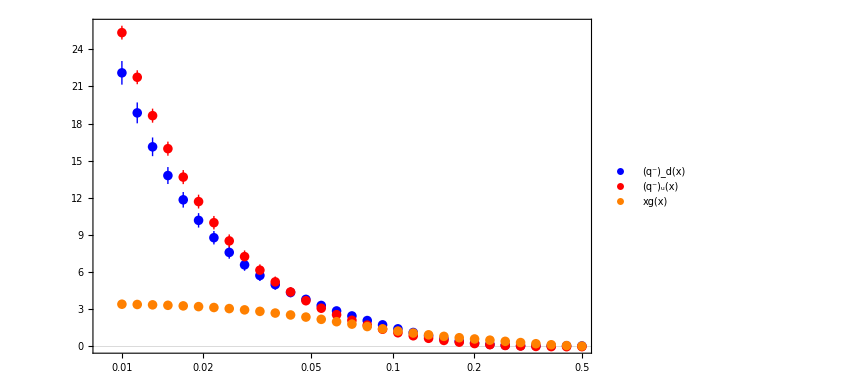

```mathematica
ListLogLinearPlot[{dbarunp,ubarunp,gunp},PlotTheme->"Scientific",PlotStyle->{Blue,Red,Orange},PlotRange->All,ImageSize->Scaled[0.2],PlotLegends->Placed[PointLegend[{Blue,Red,Orange},{"(q^-)_d(x)","(q^-)_u(x)","xg(x)"}],{0.8,0.8}]]
```

```mathematica
dfl=1;
dVpol=ParallelTable[{x,Around[pdfJAM22PolCentral[dfl,x,testq]-pdfJAM22PolCentral[-dfl,x,testq],Sqrt[pdfJAM22PolErr[dfl,x,testq]^2+pdfJAM22PolErr[-dfl,x,testq]]]},{x,logrange}];
ufl =2;
uVpol=ParallelTable[{x,Around[pdfJAM22PolCentral[ufl,x,testq]-pdfJAM22PolCentral[-ufl,x,testq],Sqrt[pdfJAM22PolErr[ufl,x,testq]^2+pdfJAM22PolErr[-ufl,x,testq]]]},{x,logrange}];

dbarfl=-1;
dbarpol=ParallelTable[{x,Around[pdfJAM22PolCentral[dbarfl,x,testq],pdfJAM22PolErr[dbarfl,x,testq]]},{x,logrange}];
ubarfl =-2;
ubarpol=ParallelTable[{x,Around[pdfJAM22PolCentral[ubarfl,x,testq],pdfJAM22PolErr[ubarfl,x,testq]]},{x,logrange}];
gfl =21;

gpol=ParallelTable[{x,x*Around[pdfJAM22PolCentral[gfl,x,testq],pdfJAM22PolErr[gfl,x,testq]]},{x,logrange}];
```

```mathematica
faz = n * x^(-α)(1-x)^(β)
```

n (1-x)^β x^-α

```mathematica
uVpol
```

{{0.01,1.41.6},{0.0121604,1.51.5},{0.0147876,1.61.4},{0.0179823,1.71.2},{0.0218672,1.81.1},{0.0265915,1.91.0},{0.0323364,2.00.9},{0.0393224,2.10.8},{0.0478176,2.20.7},{0.0581482,2.30.5},{0.0707107,2.40.4},{0.0859871,2.500.31},{0.104564,2.550.23},{0.127154,2.560.26},{0.154625,2.500.32},{0.18803,2.40.4},{0.228653,2.20.4},{0.278051,1.80.4},{0.338122,1.40.4},{0.41117,1.010.31},{0.5,0.580.24}}

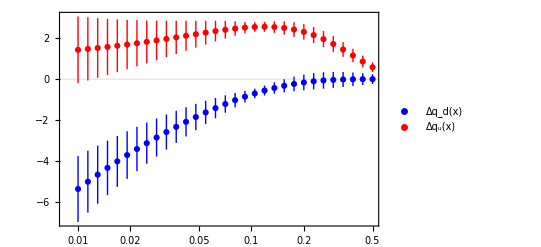

```mathematica
plt1=ListLogLinearPlot[{dVpol,uVpol},PlotTheme->"Scientific",PlotStyle->{Blue,Red},PlotRange->All,ImageSize->Scaled[0.2],PlotLegends->Placed[PointLegend[{Blue,Red},{"Δq_d(x)","Δq_u(x)"}],{0.8,0.3}]]
```

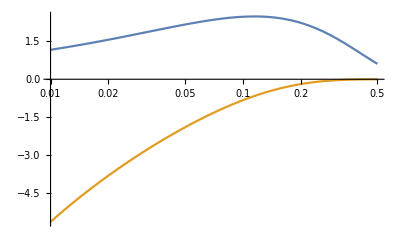

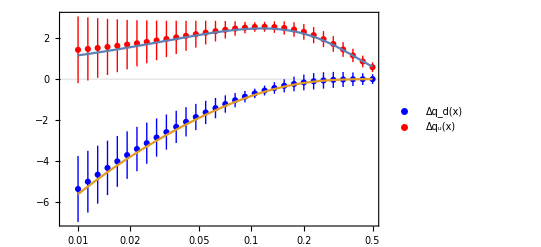

```mathematica
plt2= LogLinearPlot[{faz/.{n->11,α->-0.48,β->3.7},faz/.{n->-0.9,α->0.42,β->10}},{x,0.01,0.5}]
Show[plt1,plt2]
```

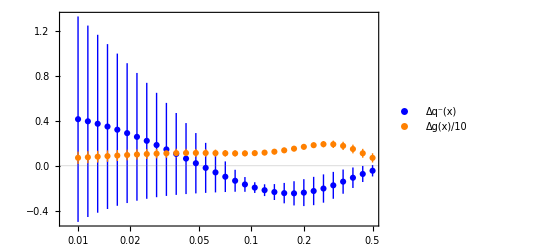

```mathematica
plt3=ListLogLinearPlot[{dbarpol,gpol},PlotTheme->"Scientific",PlotStyle->{Blue,Orange},PlotRange->All,ImageSize->Scaled[0.2],PlotLegends->Placed[PointLegend[{Blue,Orange},{"Δq^-(x)","Δg(x)/10"}],{0.8,0.8}]]
```

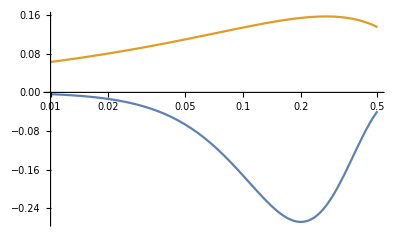

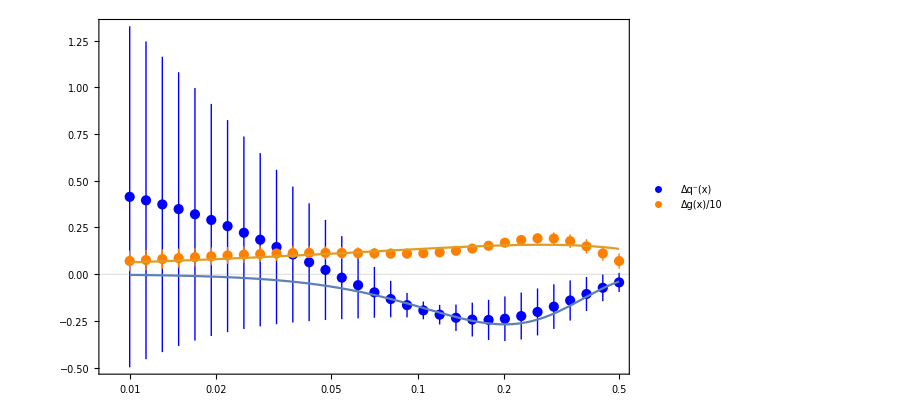

```mathematica
plt4= LogLinearPlot[{faz/.{n->-40,α->-2,β->8},faz/.{n->0.35,α->-0.37,β->1}},{x,0.01,0.5}]
Show[plt3,plt4]
```

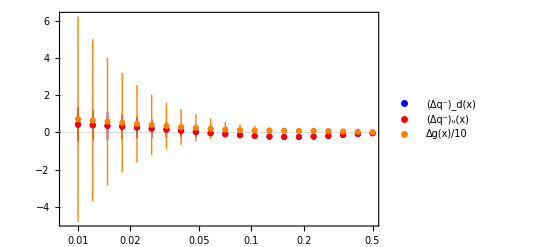

```mathematica
ListLogLinearPlot[{dbarpol,ubarpol,gpol},PlotTheme->"Scientific",PlotStyle->{Blue,Red,Orange},PlotRange->All,ImageSize->Scaled[0.2],PlotLegends->Placed[PointLegend[{Blue,Red,Orange},{"(Δq^-)_d(x)","(Δq^-)_u(x)","Δg(x)/10"}],{0.8,0.8}]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["./PDFDATA/dV_Unp.csv",{#[[1]],#[[2,1]],#[[2,2]]}& /@dVunp]
Export["./PDFDATA/uV_Unp.csv",{#[[1]],#[[2,1]],#[[2,2]]}& /@uVunp]
Export["./PDFDATA/dbar_Unp.csv",{#[[1]],#[[2,1]],#[[2,2]]}& /@dbarunp]
Export["./PDFDATA/ubar_Unp.csv",{#[[1]],#[[2,1]],#[[2,2]]}& /@ubarunp]
Export["./PDFDATA/g_Unp.csv",{#[[1]],#[[2,1]],#[[2,2]]}& /@gunp]

Export["./PDFDATA/dV_Pol.csv",{#[[1]],#[[2,1]],#[[2,2]]}& /@dVpol]
Export["./PDFDATA/uV_Pol.csv",{#[[1]],#[[2,1]],#[[2,2]]}& /@uVpol]
Export["./PDFDATA/qbar_Pol.csv",{#[[1]],#[[2,1]],#[[2,2]]}& /@ubarpol]
Export["./PDFDATA/g_Pol.csv",{#[[1]],#[[2,1]],#[[2,2]]}& /@gpol]
```

/Volumes/GoogleDrive/我的云端硬盘/jam22polJets-main

./PDFDATA/dV_Unp.csv

./PDFDATA/uV_Unp.csv

./PDFDATA/dbar_Unp.csv

./PDFDATA/ubar_Unp.csv

./PDFDATA/g_Unp.csv

./PDFDATA/dV_Pol.csv

./PDFDATA/uV_Pol.csv

./PDFDATA/qbar_Pol.csv

./PDFDATA/g_Pol.csv